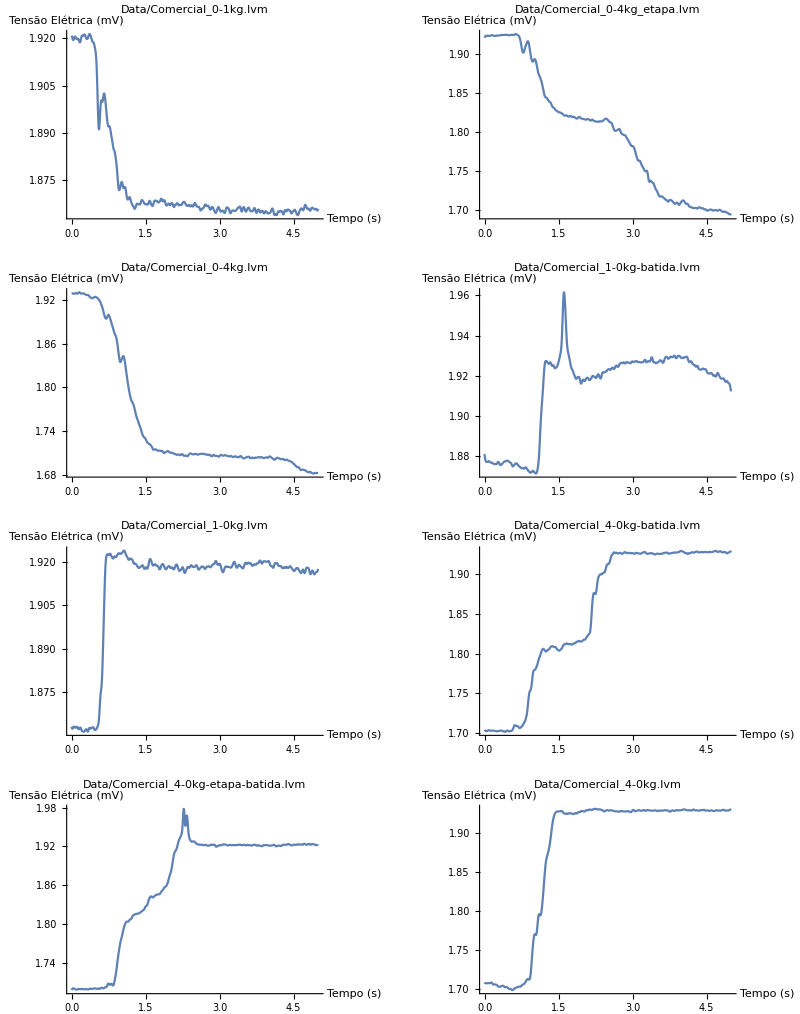

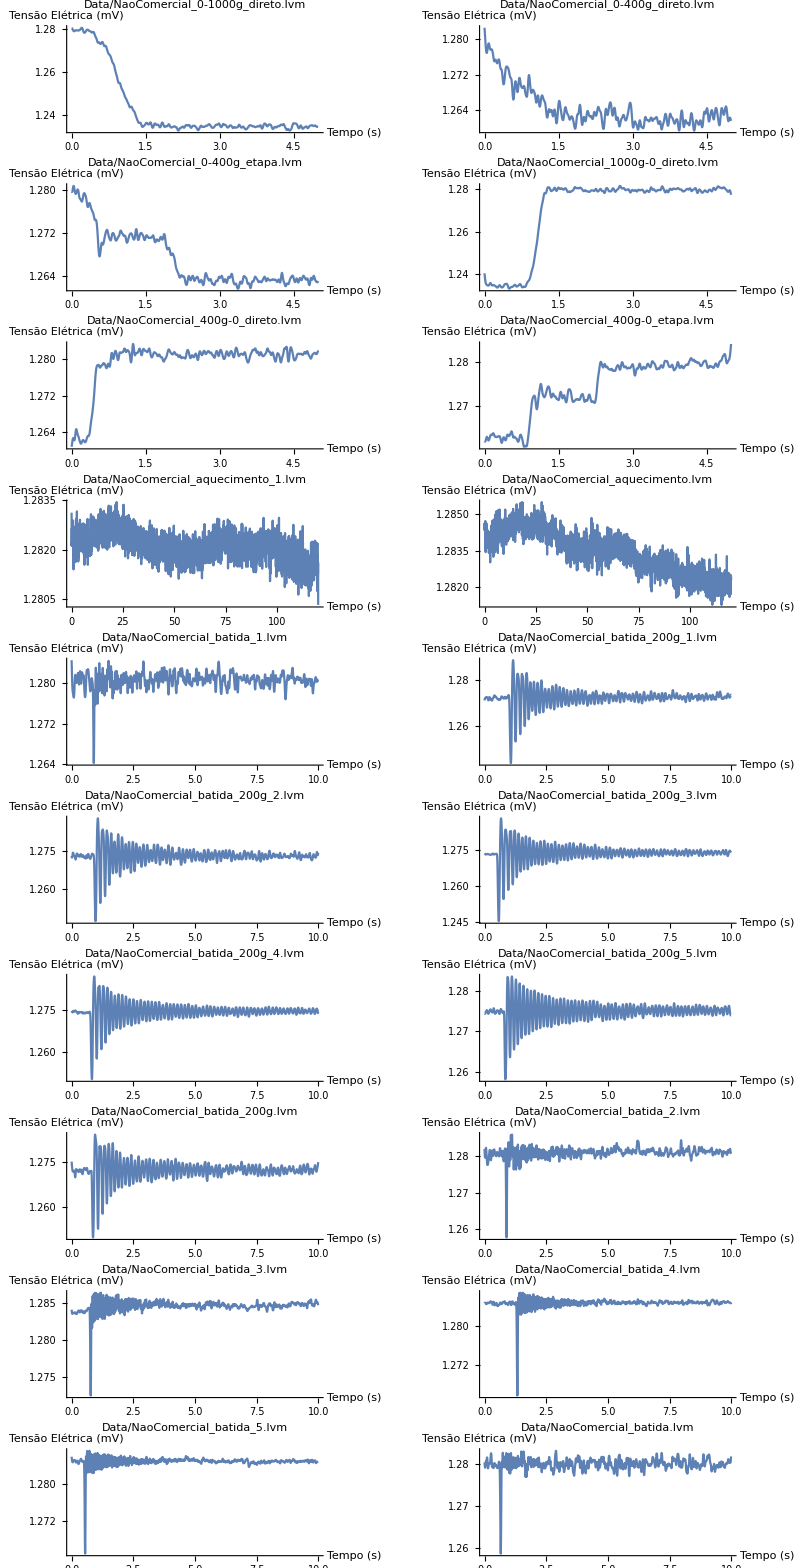

```mathematica
SetDirectory[NotebookDirectory[]<>".."];

DoProcessing[file_]:=(
data=Import[file, "TSV",NumberPoint->","];
frequency=1/(data[[2, 1]]-data[[1, 1]]);
data[[All, 2]]=LowpassFilter[data[[All, 2]], 40/frequency];
ListPlot[data, Joined->True, PlotLabel->file, PlotRange->Full, AxesLabel->{"Tempo (s)", "Tensão Elétrica (mV)"}]
);

fileList=FileNames["Data/Comercial_*.lvm"];
plots=ParallelMap[DoProcessing[#]&, fileList];
Export["Images/Comercial.pdf",GraphicsGrid[Partition[plots, 2], ImageSize->1080*2]];
GraphicsGrid[Partition[plots, 2], ImageSize->Full]


fileList=FileNames["Data/NaoComercial_*.lvm"];
plots=ParallelMap[DoProcessing[#]&, fileList];
Export["Images/NaoComercial.pdf",GraphicsGrid[Partition[plots, 2], ImageSize->1080*2]];
GraphicsGrid[Partition[plots, 2], ImageSize->Full]
```